```mathematica
Phi4 energy

Start with a free energy at the 4th order to obtain the corrections
```

```mathematica
eorigin[m_,J_,u_]:= -J m^2/2 - u m^4/4;(*initial free energy to the 4th power*)
```

```mathematica
entropy[m_]:= -(1+ m)/2 Log[(1+m)/2] - (1-m)/2 Log[(1-m)/2 ]
```

#### write the magnetization in terms of two species

```mathematica
mtot= m0 (1-x) + x mh; (*write the magnetization as m= (1-x) m_o + x mhidden and integrate out the hidden system*)
```

```mathematica
mtot
```

m0 (1-x)+m x

```mathematica
energyExpanded=eorigin[m,J,u] /. m -> mtot //Simplify (* Write the free energy in terms of m and m0*)
```

-1/2 J (m0-m0 x+mh x)^2-1/4 u (m0-m0 x+mh x)^4

```mathematica
entropy[m]/. m-> mtot -(1-x) m
```

-1/2 (1+m (1-x)-m0 (1-x)-mh x) Log[1/2 (1+m (1-x)-m0 (1-x)-mh x)]+1/2 (-1+m (1-x)-m0 (1-x)-mh x) Log[1/2 (1-m (1-x)+m0 (1-x)+mh x)]

```mathematica
freeExpanded=entropy[m]-(1-x) entropy[m0]- (x) entropy[mh]/. m-> mtot//FullSimplify
```

1/2 (-(1-x) (Log[4]+(-1+m0) Log[1-m0]-(1+m0) Log[1+m0])-x (Log[4]+(-1+mh) Log[1-mh]-(1+mh) Log[1+mh])+(-1+m0-m0 x+mh x) Log[1/2 (1+m0 (-1+x)-mh x)]+(-1+m0 (-1+x)-mh x) Log[1/2 (1+m0-m0 x+mh x)])

#### Compute the derivative of the free energy as function of the hidden variable m and divided by x and define the saddle point equation for mhidden

```mathematica
(*saddle point equation for the magnetization of the hidden system as a function of m0*)
```

```mathematica
crossentropy[m_,m0_,x_]:=SeriesCoefficient[entropy[m0(1-x) +m x ] -(1-x) entropy[m0]- x entropy[m ],{x,0,1}]//Simplify
```

```mathematica
D[crossentropy[m,m0,x],m]//Simplify
```

1/2 (-Log[1-m]+Log[1+m]+Log[1-m0]-Log[1+m0])

```mathematica
denergy[x_,J_,u_,m0_,m_]=D[eorigin[(1-x)m0+x m,J,u]/x,m]//Simplify
```

(m0 (-1+x)-m x) (J+u (m0 (-1+x)-m x)^2)

```mathematica
mhat[m,m0,J,x,u]= Tanh[-1/2 denergy[x,J,u,m0,m] - (Log[1-m0]-Log[1+m0])/4 ]//Simplify
```

-Tanh[1/4 (2 (m0 (-1+x)-m x) (J+u (m0 (-1+x)-m x)^2)+Log[1-m0]-Log[1+m0])]

```mathematica
Series[mhat[m,m0,J,x,u],{m,0,2}]
```

-Tanh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])]+(1/2 (J x+3 m0^2 u x-6 m0^2 u x^2+3 m0^2 u x^3)+1/2 (-J x-3 m0^2 u x+6 m0^2 u x^2-3 m0^2 u x^3) Tanh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])]^2) m+(-Sech[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])] (3/2 (-m0 u x^2+m0 u x^3) Cosh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])]+1/8 (-J x-3 m0^2 u x+6 m0^2 u x^2-3 m0^2 u x^3)^2 Sinh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])])+1/4 (-J x-3 m0^2 u x+6 m0^2 u x^2-3 m0^2 u x^3)^2 Tanh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])]-Tanh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])] (-Sech[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])] (1/8 (-J x-3 m0^2 u x+6 m0^2 u x^2-3 m0^2 u x^3)^2 Cosh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])]+3/2 (-m0 u x^2+m0 u x^3) Sinh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])])+1/4 (-J x-3 m0^2 u x+6 m0^2 u x^2-3 m0^2 u x^3)^2 Tanh[1/4 (-2 J m0-2 m0^3 u+2 J m0 x+6 m0^3 u x-6 m0^3 u x^2+2 m0^3 u x^3+Log[1-m0]-Log[1+m0])]^2)) m^2+O[m]^3

```mathematica
mhat1[m_,m0_,J_,x_,u_]:=-Tanh[(m0 (-1+x)-m x) (J+u (m0 (-1+x)-m x)^2)]
```

```mathematica
mhat1[m_,m0_,J_,x_,u_]:=-Tanh[1/2 (m0 (-1+x)-m x) (J+u (m0 (-1+x)-m x)^2) + 1/4 Log[1+ m0]-1/4 Log[1-m0]]
```

```mathematica
Do an  expansion order by order to obtain mhat as a function of m_obs up to 4th order
```

```mathematica
mexp[y1_,y2_,y3_,y4_,m0_]:=  y1 m0 + y2 m0^2 +y3 m0^3 + y4 m0^4
mexp[y1,y2,y3,y4,m0]
```

m0 y1+m0^2 y2+m0^3 y3+m0^4 y4

```mathematica
mhat1[mexp[y1,y2,y3,y4,m0],m0,J,x,u]
```

-Tanh[(m0 (-1+x)-x (m0 y1+m0^2 y2+m0^3 y3+m0^4 y4)) (J+u (m0 (-1+x)-x (m0 y1+m0^2 y2+m0^3 y3+m0^4 y4))^2)]

```mathematica
Series[mhat1[mexp[y1,y2,y3,y4,m],m,J,x,u],{m,0,4}]//Simplify
```

J (1+x (-1+y1)) m+J x y2 m^2+(u (1+x (-1+y1))^3+1/3 J^3 (-1+x-x y1)^3+J x y3) m^3+x (-J^3 (1+x (-1+y1))^2 y2+3 u (1+x (-1+y1))^2 y2+J y4) m^4+O[m]^5

```mathematica
Order by order idenfity m= s1 m0 + s2 m0^2 + s3 m0^3 +s4 m0^4
```

```mathematica
s1
```

```mathematica
s1
```

s1

```mathematica
z1[y1_,y2_,y3_,y4_,J_ ,x_,u_]:=SeriesCoefficient[mhat1[mexp[y1,y2,y3,y4,m0],m0,J,x,u],{m0,0,1}]
x1[J_,x_,u_]:=a/.Solve[a==z1[a,b,c,d,J,x,u],a]
x1[J,x,u][[1]]
s1[J_,x_,u_]:=x1[J,x,u][[1]]
```

(-J+J x)/(-1+J x)

### s2

```mathematica
z2[y1_,J_ ,x_,J4_]:=SeriesCoefficient[mhat1[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,2}]
x2[J_,x_,J4_]:=y2/. Solve[y2== z2[s1[J,x,J4],J,x,J4],y2]
s2[J_,x_,J4_]:= x2[J,x,J4][[1]] // Simplify
s2[J,x,J4]
```

0

### s3

```mathematica
z3[y1_,y2_,J_ ,x_,J4_]:=SeriesCoefficient[mhat1[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,3}]
x3[J_,x_,J4_]:=y3/. Solve[y3== z3[s1[J,x,J4],0,J,x,J4],y3]
s3[J_,x_,J4_]:= x3[J,x,J4][[1]] // Simplify
s3[J,x,J4]
```

((J^3-3 J4) (-1+x)^3)/(3 (-1+J x)^4)

```mathematica
s3[1,x,u]
```

(1-3 u)/(3 (-1+x))

```mathematica
z4[y1_,y2_,y3_,J_ ,x_,J4_]:=SeriesCoefficient[mhat1[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,4}]
x4[J_,x_,J4_]:=y4/. Solve[y4== z4[s1[J,x,J4],0,s3[J,x,J4],J,x,J4],y4]
s4[J_,x_,J4_]:= x4[J,x,J4][[1]] // Simplify
s4[J,x,J4]
```

0

## Compute the free energy at the saddle point and expand in terms of mobserved

```mathematica
(* remember x s(mhat) = -x/2 log( (1 - mhat^2)/4) + x/2 mhat atanh(mhat) *)
```

```mathematica
crossentropy[m_,m0_,x_]:= x SeriesCoefficient[entropy[m0(1-x) +m x ] -(1-x) entropy[m0]- x entropy[m ],{x,0,1}]//Simplify
```

```mathematica
Normal[Series[Crossentropy[m,m0]/. m -> s1[J,x,u] m0 +s3[J,x,u] m0^3,{m0,0,4}]/(1-x)//Simplify ]/.J -> 1
```

0

```mathematica
energytot[m_,m0_,J_,u_,x_]:= eorigin[(1-x)m0+ x m,J,u]  +  x/2  Log[1-m^2] -  m   x denergy[x,J,u,m0,m]   (*entropy is computed at mhat )*)

(*adding the cross entropy term*)
freeenergytotNEW[m_,m0_,J_,u_,x_]:= eorigin[(1-x)m0+ x m,J,u]  +  x/2  Log[1-m^2] -  m   x denergy[x,J,u,m0,m]  - crossentropy[m,m0,x] (*entropy is computed at mhat )*)
```

```mathematica
energytot[s1[J,x,u] m0+s3[J,x,u]m0^3,m0,J,u,x]//Simplify
```

1/4 (-2 J (m0-m0 x+x ((m0^3 (J^3-3 u) (-1+x)^3)/(3 (-1+J x)^4)+(J m0 (-1+x))/(-1+J x)))^2-u (m0-m0 x+x ((m0^3 (J^3-3 u) (-1+x)^3)/(3 (-1+J x)^4)+(J m0 (-1+x))/(-1+J x)))^4-4 x ((m0^3 (J^3-3 u) (-1+x)^3)/(3 (-1+J x)^4)+(J m0 (-1+x))/(-1+J x)) (m0 (-1+x)-x ((m0^3 (J^3-3 u) (-1+x)^3)/(3 (-1+J x)^4)+(J m0 (-1+x))/(-1+J x))) (J+u (m0 (-1+x)-x ((m0^3 (J^3-3 u) (-1+x)^3)/(3 (-1+J x)^4)+(J m0 (-1+x))/(-1+J x)))^2)+2 x Log[1-((m0^3 (J^3-3 u) (-1+x)^3)/(3 (-1+J x)^4)+(J m0 (-1+x))/(-1+J x))^2])

```mathematica
energytotNEW[s1[J,x,u] m0,m0,J,u,x]//Simplify
```

1/4 (-(m0^4 u (-1+x)^4)/(-1+J x)^4-(2 J m0^2 (-1+x)^2)/(-1+J x)^2+(4 J m0^2 (-1+x)^2 x (J+m0^2 u (-1+x)^2-2 J^2 x+J^3 x^2))/(-1+J x)^4-2 x ((-1+J m0) Log[1-m0]-(1+J m0) Log[1+m0]+Log[1-J m0]-J m0 Log[1-J m0]+Log[1+J m0]+J m0 Log[1+J m0])+2 x Log[1-(J^2 m0^2 (-1+x)^2)/(-1+J x)^2])

```mathematica
(*Series[-J  m0^2(1-x)/2 - J4 (1-x)^3/4 m0^4+  x /(1-x)  f[s1[J,x,J4] m0+s3[J,x,J4]m0^3,m0,J,J4,x],{m0,0,4}]//Simplify
```

```mathematica
(*Expand the free energy f1 around the solution mhat=s1 m0 + s3 m0^3 up to the 4th power*)
```

```mathematica
Series[ freeenergytotNEW[s1[J,x,u] m + s3[J,x,u] m^3 ,m,J,u,x]/(1-x) - entropy[m],{m,0,4}]//Simplify
```

-Log[2]+((-1+J) (-1-(-2+J) x+(-1+J) J x^2) m^2)/(2 (-1+x) (-1+J x))+1/(12 (-1+x) (-1+J x)^4)(-1+(4+4 J^3-4 J^4) x+2 J (-8+5 J-6 J^3+6 J^4) x^2-2 J^2 (-12+10 J+3 J^2-12 J^3+9 J^4) x^3+J^3 (-16+19 J-16 J^3+12 J^4) x^4+J^4 (3-4 J+4 J^3-3 J^4) x^5+3 u (1+4 (-2+J) x+(6+16 J-16 J^2) x^2+4 (-1-6 J^2+6 J^3) x^3+(1+16 J^3-16 J^4) x^4+4 (-1+J) J^4 x^5)) m^4+O[m]^5

```mathematica
J2prova=(1-J^3 x^2+J^2 x (1+2 x)+J (1-5 x+x^2))/(2 ((-1+x) (-1+J x)))
```

(1-J^3 x^2+J^2 x (1+2 x)+J (1-5 x+x^2))/(2 (-1+x) (-1+J x))

```mathematica
J2prova/. J -> 1//Simplify
```

1

```mathematica
J4prova=-1/(3 (-1+x) (-1+J x)^4)(-1+(4+4 J^3-4 J^4) x+2 J (-8+5 J-6 J^3+6 J^4) x^2-2 J^2 (-12+10 J+3 J^2-12 J^3+9 J^4) x^3+J^3 (-16+19 J-16 J^3+12 J^4) x^4+J^4 (3-4 J+4 J^3-3 J^4) x^5+3 u (1+4 (-2+J) x+(6+16 J-16 J^2) x^2+4 (-1-6 J^2+6 J^3) x^3+(1+16 J^3-16 J^4) x^4+4 (-1+J) J^4 x^5))
```

-1/(3 (-1+x) (-1+J x)^4)(-1+(4+4 J^3-4 J^4) x+2 J (-8+5 J-6 J^3+6 J^4) x^2-2 J^2 (-12+10 J+3 J^2-12 J^3+9 J^4) x^3+J^3 (-16+19 J-16 J^3+12 J^4) x^4+J^4 (3-4 J+4 J^3-3 J^4) x^5+3 u (1+4 (-2+J) x+(6+16 J-16 J^2) x^2+4 (-1-6 J^2+6 J^3) x^3+(1+16 J^3-16 J^4) x^4+4 (-1+J) J^4 x^5))

```mathematica
J4prova /. {J -> 1, u-> 1/3}//Simplify
```

0

```mathematica
J2new[J_,J4_,x_]:=-2 (J-J x)/(-2+2 J x)
```

```mathematica
J4new[J_,J4_,x_]:= 4 ((-1+x)^3 (-3 J4+J^4 x))/(12 (-1+J x)^4)
```

```mathematica
J4new[1,J4,x]
```

(-3 J4+x)/(3 (-1+x))

```mathematica
Limit[J4new[1,J4,x], J4 -> .1]  //Simplify
```

(-0.1+0.333333 x)/(-1.+x)

```mathematica
entropy[m_]:= -(1-m)/2 Log[(1-m)/2] - (1+m)/2 Log[(1+m)/2]
```

```mathematica
Series[entropy[m],{m,0,4}]
```

Log[2]-m^2/2-m^4/12+O[m]^5

```mathematica
Manipulate[Plot[{J4new[J,J4,x]/J4  , J2new[J,J4,x]/J},{x,0,1}],{J,0.001,1},{J4,0.00,10}]
```

```mathematica
beta[J_,J4_,x_]:= - (1-x) D[Log[J4new[J,J4,x] ],x] //Simplify
```

```mathematica
beta[J,J4,x]+(1- J2new[J,J4,x])//Simplify
```

0

```mathematica
beta[J,J4,x] -3(1- J2new[J,J4,x])+J2new[J,J4,x] (1- J2new[J,J4,x]^3/(3 J4new[J,J4,x]))//Simplify
```

0

```mathematica
beta[J,J4,x]//Simplify
```

(1-J)/((-1+x) (-1+J x))

```mathematica
J-J2new[J,J4,x]//Simplify
```

((-1+J) J x)/(-1+J x)

```mathematica
Series[Log[(1-Tanh[e+x a]^2)/4],{x,0,4}]
```

Log[1/4-Tanh[e]^2/4]-2 (a Tanh[e]) x+(-a^2+a^2 Tanh[e]^2) x^2-2/3 (-a^3 Tanh[e]+a^3 Tanh[e]^3) x^3+1/6 (a^4-4 a^4 Tanh[e]^2+3 a^4 Tanh[e]^4) x^4+O[x]^5

```mathematica
Series[Log[(1-Tanh[a m+b m^3]^2)],{m,0,4}]
```

-a^2 m^2+(a^4/6-2 a b) m^4+O[m]^5

```mathematica
Solve[ 3(1-x) +x (1-x^3/(3y))-1==0,y]
```

{{y→-x^4/(6 (-1+x))}}

```mathematica
F[x_,y_]:=3(1-x) +x (1-x^3/(3y))-1
```

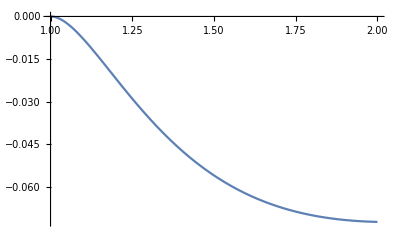

```mathematica
Plot[F[x,-x^4/(6 (-1+x))-0.1],{x,1,2}, PlotRange->Automatic]
```

```mathematica
Series[Log[Cosh[x]],{x,0,4}]
```

x^2/2-x^4/12+O[x]^5

```mathematica
Series[entropy[m0 (1-x) ],{x,0,2}]//Simplify
```

1/2 (Log[4]+(-1+m0) Log[1-m0]-(1+m0) Log[1+m0])+1/2 m0 (-Log[1-m0]+Log[1+m0]) x+(m0^2 x^2)/(2 (-1+m0^2))+O[x]^3

```mathematica
Normal[Series[entropy[m0 (1-x) ],{x,0,1}]//Simplify]-Normal[Series[(1-x) entropy[m0 ],{x,0,1}]//Simplify]//Simplify
```

-1/2 x (Log[(1-m0)/4]+Log[1+m0])

```mathematica
Atanh[x]
```

Atanh[x]

```mathematica
Series[x entropy[m  ],{x,0,2}]-Series[entropy[x m],{x,0,2}]
```

-Log[2]+(-1/2 (1-m) Log[(1-m)/2]+1/2 (-1-m) Log[(1+m)/2]) x+(m^2 x^2)/2+O[x]^3

```mathematica
Series[entropy[x m],{x,0,2}]
```

Log[2]-(m^2 x^2)/2+O[x]^3